```mathematica
Findsegment[xs_,x_]:=
Module[{k},
k=1;
While[(xs[[k]]<  x)&&(xs[[k+1]]≤  x),
k++];
k]
```

```mathematica
SolveTridiag[a_,b_,c_,d_]:=
Module[{x,n,k,mu,a1,d1},
a1=a;
d1=d;
n=Length[a];
For[k=1,k≤n-1,k++,
mu=-c[[k]]/a1[[k]];
a1[[k+1]]+=mu*b[[k]];
d1[[k+1]]+= mu* d1[[k]];];
x=Table[0,{n}];
x[[n]]=d1[[n]]/a1[[n]];
For[k=(n-1),k≥1,k--,
x[[k]]=(d1[[k]]-(b[[k]]*x[[k+1]]))/a1[[k]]];
x]
```

```mathematica
CubicSpline[xs_,as_,bs_,cs_,ds_,x_]:=
Module[{a,b,s,t},
a=Findsegment[xs,x];
t=x-xs[[a]];
s=as[[a]]+(bs[[a]]*t)+(cs[[a]]*t^2)+(ds[[a]]*t^3);
s]
```

```mathematica
CoefsCubicSpline[xs_,ys_]:=
Module[{bs1,bs2,cs1,a,b,c,d,as,bs,cs,ds,k,j,h,n,a1,b1,d1},
n=Length[xs]-1;
as=ys;
bs=Table[0,{n}];
ds=Table[0,{n}];
a={1};b={0}; d={0};
h=Table[xs[[i+1]]-xs[[i]],{i,1,n}];
For[k=1,k≤n-1,k++,a1=2*(h[[k+1]]+h[[k]]);AppendTo[a,a1]];
AppendTo[a,1];
For[k=1,k≤n-1,k++,b1=h[[k+1]];AppendTo[b,b1]];
c=Table[h[[i]],{i,1,n-1}];
AppendTo[c,0];
For[k=1,k≤n-1,k++,d1=(((3/h[[k+1]])*(as[[k+2]]-as[[k+1]]))-((3/h[[k]])*(as[[k+1]]-as[[k]])));AppendTo[d,d1]];
AppendTo[d,0];
cs1=SolveTridiag[a,b,c,d];
cs=Table[cs1[[i]],{i,1,n}];
For[k=n,k≥ 1,k--,
bs1=((1/h[[k]])*(as[[k+1]]-as[[k]]));
bs2=((h[[k]]/3)*((2*cs1[[k]])+cs1[[k+1]]));
bs[[k]]=bs1-bs2;
ds[[k]]=(cs1[[k+1]]-cs1[[k]])/(3*h[[k]]);];
{as,bs,cs,ds}]
```

```mathematica
xs={0,1.5,3,4,5,7};
ys=Map[Sin,xs];
```

```mathematica
{as,bs,cs,ds}=CoefsCubicSpline[xs,ys];
```

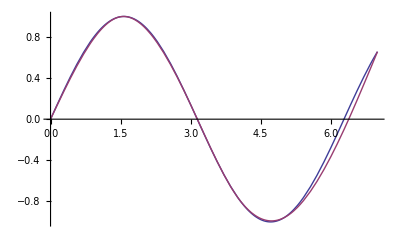

```mathematica
Plot[{Sin[x],CubicSpline[xs,as,bs,cs,ds,x]},{x,0,7}]
```

```mathematica
f[x1_]:=(-Sin[x1]+100*x1)*0.01Cos[x1];
xsv1={5,9,9.5,11,12.5,13.7,14.8,15.2,16.2,17.6,18.7,19.3,20};
ysv1=Map[f,xsv1];
```

```mathematica
{asv,bsv,csv,dsv}=CoefsCubicSpline[xsv1,ysv1];
```

```mathematica
q1=Plot[f[x],{x,5,20},PlotStyle->Orange];
```

```mathematica
q2=Plot[CubicSpline[xsv1,asv,bsv,csv,dsv,x],{x,5,20},PlotStyle->Purple];
```

```mathematica
q3=ListPlot[Transpose[{xsv1,ysv1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[q1,q2,q3]
```

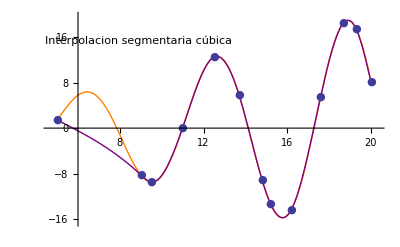

```mathematica
xp0={0,6,19,26,31,35,36};
yp0={13,8,-2,-4.2,-3.3,-1,0};
{as0,bs0,cs0,ds0}=CoefsCubicSpline[xp0,yp0];
```

```mathematica
g0=Plot[CubicSpline[xp0,as0,bs0,cs0,ds0,x],{x,0,36},PlotRange->{-10,22},PlotStyle->Red];
r0=ListPlot[Transpose[{xp0,yp0}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp1={0,6,13,19,21,25,27.2,33.2,36};
yp1={0,8,13,15,15,14,13,7,0};
{as1,bs1,cs1,ds1}=CoefsCubicSpline[xp1,yp1];
```

```mathematica
g1=Plot[CubicSpline[xp1,as1,bs1,cs1,ds1,x],{x,0,36},PlotStyle->Red];
r1=ListPlot[Transpose[{xp1,yp1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp2={19,20,21.5,24,25};
yp2={15,17,20,16,14};
{as2,bs2,cs2,ds2}=CoefsCubicSpline[xp2,yp2];
```

```mathematica
g2=Plot[CubicSpline[xp2,as2,bs2,cs2,ds2,x],{x,19,25},PlotStyle->Orange];
r2=ListPlot[Transpose[{xp2,yp2}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp3={21,22.2,24.9,25.9,27};
yp3={5,7.2,9.9,7,5};
{as3,bs3,cs3,ds3}=CoefsCubicSpline[xp3,yp3];
```

```mathematica
g3=Plot[CubicSpline[xp3,as3,bs3,cs3,ds3,x],{x,21,27},PlotStyle->Brown];
r3=ListPlot[Transpose[{xp3,yp3}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp4={31,31.3,32.1,35};
yp4={-3.3,-1.4,-0.3,-1};
{as4,bs4,cs4,ds4}=CoefsCubicSpline[xp4,yp4];
```

```mathematica
g4=Plot[CubicSpline[xp4,as4,bs4,cs4,ds4,x],{x,30.5,35},PlotStyle->Black];
r4=ListPlot[Transpose[{xp4,yp4}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp5={0,1,1.2};
yp5={0,4.5,6};
{as5,bs5,cs5,ds5}=CoefsCubicSpline[xp5,yp5];
```

```mathematica
g5=Plot[CubicSpline[xp5,as5,bs5,cs5,ds5,x],{x,0,1.2},PlotStyle->Red];
r5=ListPlot[Transpose[{xp5,yp5}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp6={1.2,0.2,0};
yp6={6,9,13};
{as6,bs6,cs6,ds6}=CoefsCubicSpline[xp6,yp6];
```

```mathematica
g6=Plot[CubicSpline[xp6,as6,bs6,cs6,ds6,x],{x,0,1.2},PlotStyle->Red];
r6=ListPlot[Transpose[{xp6,yp6}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[g0,g1,g2,g3,g4,g5,g6,r0,r1,r2,r3,r4,r5,r6]
```

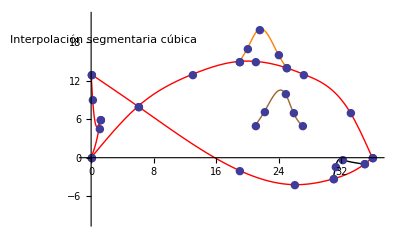

```mathematica
xs0={8.5,9,10,10.6};
ys0={3.5,5.3,5.2,4};
{asv0,bsv0,csv0,dsv0}=CoefsCubicSpline[xs0,ys0];
```

```mathematica
h0=Plot[CubicSpline[xs0,asv0,bsv0,csv0,dsv0,x],{x,8.5,10.6},PlotStyle->Red];
k0=ListPlot[Transpose[{xs0,ys0}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xs1={8.5,9,10.1,12.3,13.6};
ys1={3.5,2,1.1,2,4.2};
{asv1,bsv1,csv1,dsv1}=CoefsCubicSpline[xs1,ys1];
```

```mathematica
h1=Plot[CubicSpline[xs1,asv1,bsv1,csv1,dsv1,x],{x,8.5,13.6},PlotStyle->Red];
k1=ListPlot[Transpose[{xs1,ys1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xs2={13,13.6};
ys2={12,4.2};
{asv2,bsv2,csv2,dsv2}=CoefsCubicSpline[xs2,ys2];
```

```mathematica
h2=Plot[CubicSpline[xs2,asv2,bsv2,csv2,dsv2,x],{x,13,13.6},PlotStyle->Red];
k2=ListPlot[Transpose[{xs2,ys2}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xs3={13,13.1,13.2};
ys3={12,14.5,17};
{asv3,bsv3,csv3,dsv3}=CoefsCubicSpline[xs3,ys3];
```

```mathematica
h3=Plot[CubicSpline[xs3,asv3,bsv3,csv3,dsv3,x],{x,13,13.2},PlotStyle->Red];
k3=ListPlot[Transpose[{xs3,ys3}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xs4={9.4,10,12,13.2};
ys4={12.3,14,16,17};
{asv4,bsv4,csv4,dsv4}=CoefsCubicSpline[xs4,ys4];
```

```mathematica
h4=Plot[CubicSpline[xs4,asv4,bsv4,csv4,dsv4,x],{x,9.4,13.2},PlotStyle->Red];
k4=ListPlot[Transpose[{xs4,ys4}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xs5={9.4,10,12,14.5,15.4};
ys5={12.3,10,9,10,12};
{asv5,bsv5,csv5,dsv5}=CoefsCubicSpline[xs5,ys5];
```

```mathematica
h5=Plot[CubicSpline[xs5,asv5,bsv5,csv5,dsv5,x],{x,9.4,15.4},PlotStyle->Red];
k5=ListPlot[Transpose[{xs5,ys5}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[h0,h1,h2,h3,h4,h5,k0,k1,k2,k3,k4,k5,PlotRange->All]
```